# Project 1 - Convolution

## Report

Emil Lengman, emillen@kth.se
Simon Enerstrand, simonene@kth.se

## Section. Summary

For this project we had three sub-assignments. The three assignments built upon each other and are specified with

### Section.Subsection Summary sub-assignment 1

This assignment is based on a dice game. There are five dice in the form of the Platonic solids (one die with 4 possible outcomes, one with 6, one with 8, one with 12, and one with 20). All dice are thrown at once, and if the sum of all dice are 10 or below, or 45 or higher, the player win a Teddy bear to bring home (each game costs 2 euro). We will:

Determine the exact probability function of the sum.

Determine the exact probability of winning the Teddy bear.

Determine the expected investment to win a Teddy.

Calculate the probability of winning at least once in twenty games.

### Section.Subsection Summary sub-assignment 2

The task is considered individually and assumes that you have full knowledge of all the material you are presenting. In order to be approved, then you have solved the task and be able to explain the entire task and solution.

To account for the task that you do not have solved is considered cheating. It is also cheating to copy the solution or part of a solution from another. If two solutions are presented as (partially) copies they are rejected both.

If the solution contains parts, e.g. background material, which you do not have produced, you must clearly indicate this and indicate the source.

Suspicion of cheating or misleading can be reported to the Disciplinary Board.

### Section.Subsection Summary sub-assignment 3

The examination is carried out according to the booking 2016-11-18.

The booking is done according to the information at KTH Social  Projektuppgifter/Projekt 1.

Please note that this project should be reported in groups of two students.

The report (including code section) should be uploaded before 2016-11-17, 08:00 according to the information at KTH Social  Projektuppgifter/Projekt 1.

A printed copy of the report must be submitted at the examination. Don’t print the code section.

Notice that the report shall always be uploaded in time even if you cannot attend at the oral presentation. In case of illness, etc., then the oral presentation may be made during project 3. If you are unable to attend, you must in advance inform the teacher (in writing).

If you ignore the oral presentation or the uploading of the report without contacting the teacher (in writing) you will have to wait for the next course for a new project exam.

asd

## Section. Winning a teddy

### Section.Subsection Probability function of the sum

#### Solution

To start off we defined the probability functions of the dice. Since the dice are perfect, all of the sides have the exact same probability of getting their face up, so we can define them as Discrete uniform distributions from 1 to the amount of faces the die has.

```mathematica
pf(k)=P(X=k)=Piecewise[{{1/m, 1≤k≤m}, {0, otherwise}}]
```

Then we performed Convolutions in order. First with die 1 and 2, then we took the result from that and convoluted it with die 3, and then 4 and lastly 5. This gave us the probability function of the sum.

#### Discussion

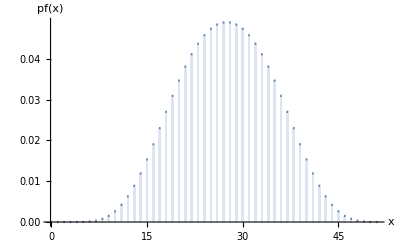

Above we have a diagram of the function

### Section.Subsection Exact probability to win Teddy

#### Solution

Now that we have the probability function of the sum of the dice, we can move on to calculate the probability of winning Teddy. We define the random variable S as the sum of the dice. We know that if S satisfies S≤10 or S≥45 you will win the Teddy. We can easily use that to calculate the probability.

```mathematica
P(X="winning teddy")= ∑_(k=5)^10 pf(k) +∑_(k=45)^50 pf(k)
```

We start at 5 because we know that it is the lowest possible outcome of the game, and stop at 50 because it is the highest.

#### Discussion

### Section.Subsection Expected investment to win Teddy

#### Solution

To calculate the expected investment we need to to know how many times we are expected to play before winning. We know that calculating the expected value for a random variable that is distributed for finding the first successful event can be done like this.

```mathematica
μ= 1/p
```

Where p is the probability of  a successful outcome.

### Section.Subsection Probability of winning Teddy in twenty games

#### Solution

We used binomial distribution to calculate the probability of winning Teddy after 20 games. We know that binomial distribution is used to calculate the probability of the random variable X which is defined as the amount of successful outcomes, while the probability of a successful outcome p, and the amount of tries n, is already defined.

pf(k)=P(X=k)=Piecewise[{{Binomial[n, k](p^k(1-p))^(n-k), 0≤k≤n}}]

#### Discussion

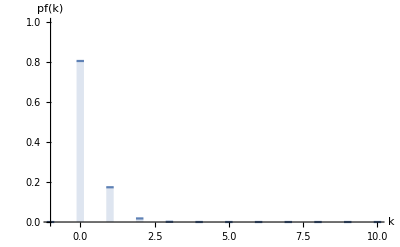

Here is a diagram of the binomial distribution function. It seems to coincide with our result (which is close 0.2). Here we can see that the chance of winning 0 times after 20 games is a little above 0.8.

## Section. Winning an electric car

Required for grade E (approved). Keep in mind that it is the mathematical method on the task that is interesting to consider, not the answer. Furthermore, solve the given task, not a variant or extension. A very good report and presentation is graded D.

Use KTH Social to discuss Mathematica code.

A general hint is to start in a small scale and test your methods with not too large numbers.

Take advantage of that you are using a mathematical programming language. Don’t “invent the wheel”.

### Winning a teddy

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.

-Graphics-

At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up.

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact (no floating point, please) probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

### Winning an electric car

At a more advanced game you invest €250 and play the five Platonic bodies ten times and count the total sum. If the sum S satisfies S≤200 or S≥350 you will an electric car worth around 0.1 M€.

Determine the exact probability of winning the car. Also give a floating point answer.

Determine the expected investment to win a car.

### Normal distribution

Since we have the exact probabilities we can compare with the approximate answer given by the normal distribution.

Determine the expectation values and standard deviations of the distributions in the Teddy and the car case.

Determine the probabilities of the Teddy prize and the car prize using the normal distribution.

Compare and comment on the results.

## Section. Normal distribution